# ASTPattern

Convert a pattern to match a corresponding CodeParser AST node

## Definition

```mathematica
ASTPattern // ClearAll;
```

### Initialization

```mathematica
Needs[ "CodeParser`" ];
```

```mathematica
Language`AddInternalContexts[ "CodeParser`*" ];
```

```mathematica
$inDef = False;
$debug = True;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::unfinished = "\
Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
ASTPattern::internal =
"An unexpected error occurred. `1`";
```

### Attributes

```mathematica
ASTPattern // Attributes = { HoldFirst };
```

### Options

```mathematica
ASTPattern // Options = { };
```

### Main definition

```mathematica
ASTPattern[ patt_ ] :=
    catchTop @ Block[ { $ContextPath },
        Needs[ "CodeParser`" ];
        With[ { p = astBlockPattern @ patt },
            checkDuplicatePatterns @ astPattern @ p
        ]
    ];
```

```mathematica
ASTPattern[ patt_, meta_ ] :=
    catchTop @ Block[ { $ContextPath },
        Needs[ "CodeParser`" ];
        With[ { p = astBlockPattern @ patt }, astPattern[ p, meta ] ]
    ];
```

```mathematica
astPattern  // ClearAll;
```

```mathematica
astPattern  // Attributes = { HoldAllComplete };
```

```mathematica
$astPattern // Attributes = { HoldAllComplete };
```

```mathematica
astPattern[ patt_ ] /; ! FreeQ[ Unevaluated @ patt, _ASTPattern ] :=
    Module[ { held, expanded, new },
        held     = HoldComplete @ patt;
        expanded = expandNestedASTPatterns @ held;
        new      = astPattern @@ expanded;
        new /. $astPattern[ a_ ] :> a
    ];
```

### Auxiliary Functions

#### FromAST

```mathematica
FromAST // beginDefinition;
```

```mathematica
FromAST[ ast_ ] := FromAST[ ast, ##1 & ];
```

```mathematica
FromAST[ ast: _LeafNode|_CallNode, wrapper_ ] :=
    ToExpression[ ToFullFormString @ ast, InputForm, wrapper ];
```

```mathematica
FromAST[ ContainerNode[ _, ast_List, _ ], wrapper_ ] :=
    FromAST[ ast, wrapper ];
```

```mathematica
FromAST[ ast_List, wrapper_ ] := FromAST[ #, wrapper ] & /@ ast;
```

```mathematica
FromAST // endDefinition;
```

#### ASTPatternTest

```mathematica
ASTPatternTest // ClearAll;
```

```mathematica
ASTPatternTest[ func_ ][ node_ ] := FromAST[ node, func ];
```

```mathematica
ASTPatternTest /: MakeBoxes[ ASTPatternTest[ f_ ], StandardForm ] :=
    With[
        {
            row = MakeBoxes[ f, StandardForm ],
            tt = MakeBoxes[ HoldForm[ ASTPatternTest ][ f ], StandardForm ],
            col = ColorData[ 97 ][ 1 ]
        },
        InterpretationBox[
            FrameBox[
                TooltipBox[ row, tt ],
                RoundingRadius -> 3,
                FrameStyle     -> col,
                FrameMargins   -> { { 4, 4 }, { 1, 1 } }
            ]
            ,
            ASTPatternTest @ f
        ]
    ];
```

#### ASTCondition

```mathematica
ASTCondition // beginDefinition;
```

```mathematica
ASTCondition // Attributes = { HoldRest };
```

```mathematica
ASTCondition[ vals_List, cond_ ] :=
    Module[ { rules, replaced },
        rules    = MapIndexed[ astCVRule, vals ];
        replaced = HoldComplete @ cond /. rules;
        ReleaseHold[ replaced /. $conditionHold[ e_ ] :> e ]
    ];
```

```mathematica
ASTCondition /: MakeBoxes[ ASTCondition[ vals_List, cond_ ], StandardForm ] :=
    Module[ { rules, replaced },
        rules = MapIndexed[ astCVBoxRule, vals ];
        replaced = HoldComplete @ cond /. rules;
        Replace[
            replaced /. $conditionHold[ e_ ] :> e,
            HoldComplete[ e_ ] :>
                With[
                    {
                        box =
                            MakeBoxes[
                                Tooltip[
                                    e,
                                    HoldForm[ ASTCondition ][ vals, cond ]
                                ],
                                StandardForm
                            ],
                        col = ColorData[ 97 ][ 2 ]
                    },
                    InterpretationBox[
                        FrameBox[
                            box,
                            RoundingRadius -> 3,
                            FrameStyle     -> col,
                            FrameMargins   -> { { 4, 4 }, { 1, 1 } }
                        ],
                        ASTCondition[ vals, cond ]
                    ]
                ]
        ]
    ];
```

```mathematica
ASTCondition // endDefinition;
```

```mathematica
$conditionHold // Attributes = { HoldAllComplete };
```

##### astCVBoxRule

```mathematica
astCVBoxRule // beginDefinition;
```

```mathematica
astCVBoxRule // Attributes = { HoldFirst };
```

```mathematica
astCVBoxRule[ node_, { pos_ } ] :=
    ASTConditionValue @ pos -> node;
```

```mathematica
astCVBoxRule // endDefinition;
```

##### astCVRule

```mathematica
astCVRule // beginDefinition;
```

```mathematica
astCVRule[ node_, { pos_ } ] :=
    ASTConditionValue @ pos -> FromAST[ node, $conditionHold ];
```

```mathematica
astCVRule // endDefinition;
```

#### EquivalentNodeQ

```mathematica
EquivalentNodeQ // beginDefinition;
```

```mathematica
EquivalentNodeQ[ nodes___ ] :=
    SameQ @@ DeleteCases[ { nodes }, KeyValuePattern[ Source -> _ ], Infinity ];
```

```mathematica
EquivalentNodeQ /: MakeBoxes[ EquivalentNodeQ[ a___ ], StandardForm ] :=
    With[
        {
            row =
                RowBox @ Riffle[
                    Cases[
                        HoldComplete @ a,
                        e_ :> MakeBoxes[ e, StandardForm ]
                    ],
                    StyleBox[
                        "≃",
                        FontColor -> Orange,
                        FontWeight -> "Heavy"
                    ]
                ],
            tt = ToBoxes @ HoldForm @ HoldForm[ EquivalentNodeQ ][ a ],
            col = ColorData[ 97 ][ 3 ]
        },
        InterpretationBox[
            FrameBox[
                TooltipBox[ row, tt ],
                RoundingRadius -> 3,
                FrameStyle -> col,
                FrameMargins -> { { 4, 4 }, { 1, 1 } }
            ]
            ,
            EquivalentNodeQ @ a
        ]
    ];
```

```mathematica
EquivalentNodeQ // endDefinition;
```

### Error cases

### Dependencies

#### Pattern

```mathematica
astPattern[ Verbatim[ Pattern ][ sym_Symbol? symbolQ, patt_ ] ] :=
    Pattern @@ Hold[ sym, astPattern @ patt ];
```

#### Special patterns

```mathematica
astPattern[ patt_ASTPattern  ] := patt;
```

```mathematica
astPattern[ patt_$astPattern ] := patt;
```

```mathematica
astPattern[ Verbatim[ Verbatim     ][ a_   ] ] := verbatimAST @ a;
```

```mathematica
astPattern[ Verbatim[ HoldPattern  ][ a_   ] ] := astPattern @ a;
```

```mathematica
astPattern[ Verbatim[ Alternatives ][ a___ ] ] :=
    Alternatives @@ (astPattern /@ HoldComplete @ a);
```

##### verbatimAST

```mathematica
verbatimAST // beginDefinition;
```

```mathematica
verbatimAST // Attributes = { HoldAllComplete };
```

```mathematica
verbatimAST[ sym_Symbol? symbolQ ] := symNamePatt @ sym;
```

```mathematica
verbatimAST[ r_Rational ] /; AtomQ @ Unevaluated @ r := rationalPattern @ r;
```

```mathematica
verbatimAST[ c_Complex  ] /; AtomQ @ Unevaluated @ c := complexPattern  @ c;
```

```mathematica
verbatimAST[ expr: _Integer|_Real|_String ] /; AtomQ @ Unevaluated @ expr :=
    leafNode[ Head @ expr, ToString[ expr, InputForm ] ];
```

```mathematica
verbatimAST[ head_[ args___ ] ] :=
    CallNode[ astPattern @ head, astPattern /@ Unevaluated @ { args }, _ ];
```

```mathematica
verbatimAST // endDefinition;
```

#### Blanks

```mathematica
astPattern[ Verbatim[ _   ] ] := callOrLeafNode[ ];
```

```mathematica
astPattern[ Verbatim[ __  ] ] := callOrLeafNode[ ]..;
```

```mathematica
astPattern[ Verbatim[ ___ ] ] := callOrLeafNode[ ]...;
```

```mathematica
astPattern[ Verbatim[ Blank             ][ sym_? symbolQ ] ] := blank @ sym;
astPattern[ Verbatim[ BlankSequence     ][ sym_? symbolQ ] ] := blank @ sym..;
astPattern[ Verbatim[ BlankNullSequence ][ sym_? symbolQ ] ] := blank @ sym...;
```

##### blank

```mathematica
blank // beginDefinition;
blank // Attributes = { HoldAllComplete };
blank[ sym_? leafHeadQ ] := callOrLeafNode[ sym | symNamePatt @ sym, _, _ ];
blank[ sym_ ] := callNode @ symNamePatt @ sym;
blank // endDefinition;
```

##### leafNode

```mathematica
leafNode // beginDefinition;
leafNode[            ] := LeafNode[ _, _, _ ];
leafNode[ a_         ] := LeafNode[ a, _, _ ];
leafNode[ a_, b_     ] := LeafNode[ a, b, _ ];
leafNode[ a_, b_, c_ ] := LeafNode[ a, b, c ];
leafNode // endDefinition;
```

##### callNode

```mathematica
callNode // beginDefinition;
callNode[            ] := CallNode[ _, _, _ ];
callNode[ a_         ] := CallNode[ a, _, _ ];
callNode[ a_, b_     ] := CallNode[ a, b, _ ];
callNode[ a_, b_, c_ ] := CallNode[ a, b, c ];
callNode // endDefinition;
```

##### callOrLeafNode

```mathematica
callOrLeafNode // beginDefinition;
callOrLeafNode[            ] := (CallNode|LeafNode)[ _, _, _ ];
callOrLeafNode[ a_         ] := (CallNode|LeafNode)[ a, _, _ ];
callOrLeafNode[ a_, b_     ] := (CallNode|LeafNode)[ a, b, _ ];
callOrLeafNode[ a_, b_, c_ ] := (CallNode|LeafNode)[ a, b, c ];
callOrLeafNode // endDefinition;
```

##### leafHeadQ

```mathematica
leafHeadQ // ClearAll;
leafHeadQ // Attributes = { HoldAllComplete };
leafHeadQ[ Complex|Integer|Rational|Real|String|Symbol ] := True;
leafHeadQ[ ___ ] := False;
```

#### Repeated

```mathematica
astPattern[ Verbatim[ Repeated ][ x_, a___ ] ] :=
    Repeated[ astPattern @ x, a ];
```

```mathematica
astPattern[ Verbatim[ RepeatedNull ][ x_, a___ ] ] :=
    RepeatedNull[ astPattern @ x, a ];
```

#### Except

```mathematica
astPattern[ Verbatim[ Except ][ c_ ] ] :=
    Except @ astPattern @ c;
```

```mathematica
astPattern[ Verbatim[ Except ][ c_, p_ ] ] :=
    Except[ astPattern @ c, astPattern @ p ];
```

#### Sequence Patterns

```mathematica
astPattern[ Verbatim[ PatternSequence ][ a___ ] ] :=
    PatternSequence @@ (astPattern /@ HoldComplete @ a);
```

#### PatternTest

```mathematica
astPattern[ Verbatim[ PatternTest ][
    Verbatim[ Pattern ][ s_Symbol? symbolQ, patt_ ],
    test_
] ] :=
    With[ { p = astPattern @ PatternTest[ patt, test ] },
        Pattern @@ HoldComplete[ s, p ]
    ];
```

```mathematica
astPattern[
    Verbatim[ PatternTest ][
        Verbatim[ Blank ][ head_? symbolQ ],
        test_
    ] ] /; leafTestQ[ head, test ] :=
    leafNode @ head;
```

```mathematica
astPattern[
    Verbatim[ PatternTest ][
        Verbatim[ BlankSequence ][ head_? symbolQ ],
        test_
    ]
] /; leafTestQ[ head, test ] :=
    leafNode @ head..;
```

```mathematica
astPattern[
    Verbatim[ PatternTest ][
        Verbatim[ BlankNullSequence ][ head_? symbolQ ],
        test_
    ]
] /; leafTestQ[ head, test ] :=
    leafNode @ head...;
```

```mathematica
astPattern[ Verbatim[ PatternTest ][ patt_, test_ ] ] :=
    With[ { p = astPattern @ patt },
        PatternTest @@ HoldComplete[ p, ASTPatternTest @ test ]
    ];
```

##### leafTestQ

```mathematica
leafTestQ // ClearAll;
```

```mathematica
leafTestQ // Attributes = { HoldAllComplete };
```

```mathematica
leafTestQ[ Integer, IntegerQ     ] := True;
leafTestQ[ Real, Developer`RealQ ] := True;
leafTestQ[ String, StringQ       ] := True;
leafTestQ[ _? leafHeadQ, AtomQ   ] := True;
leafTestQ[ ___                   ] := False;
```

#### Atoms

```mathematica
astPattern[ sym_Symbol? symbolQ ] := symNamePatt @ sym;
```

```mathematica
astPattern[ r_Rational ] /; AtomQ @ Unevaluated @ r := rationalPattern @ r;
```

```mathematica
astPattern[ c_Complex  ] /; AtomQ @ Unevaluated @ c := complexPattern  @ c;
```

```mathematica
astPattern[ expr: _Integer|_Real|_String ] /; AtomQ @ Unevaluated @ expr :=
    leafNode[ Head @ expr, ToString[ expr, InputForm ] ];
```

##### rationalPattern

```mathematica
rationalPattern // beginDefinition;
```

```mathematica
rationalPattern[ r_ ] := rationalPattern[ Numerator @ r, Denominator @ r ];
```

```mathematica
rationalPattern[ n_, d_ ] :=
    Module[ { na, da, mo, pw },
        na = astPattern @ n;
        da = astPattern @ d;
        mo = leafNode[ Integer, "-1" ];
        pw = callNode[ symbolNode[ "Power" ], { da, mo } ];
        callNode[ symbolNode[ "Times" ], { na, pw } ]
    ];
```

```mathematica
rationalPattern // endDefinition;
```

##### complexPattern

```mathematica
complexPattern // beginDefinition;
```

```mathematica
complexPattern[ c_ ] := complexPattern[ Re @ c, Im @ c ];
```

```mathematica
complexPattern[ r_, i_ ] :=
    Module[ { ra, ia, im },
        ra = astPattern @ r;
        ia = astPattern @ i;
        im = callNode[ symbolNode[ "Times" ], { ia, symbolNode[ "I" ] } ];
        callNode[ symbolNode[ "Plus" ], { ra, im } ]
    ];
```

```mathematica
complexPattern // endDefinition;
```

#### Condition

```mathematica
astPattern[ Verbatim[ Condition ][ patt_, test_ ] ] :=
    makeASTCondition[ patt, test ] /.
        $ASTCondition[ { }, cond_ ] :> cond  /.
            $ASTCondition -> ASTCondition;
```

##### makeASTCondition

```mathematica
makeASTCondition // beginDefinition;
```

```mathematica
makeASTCondition // Attributes = { HoldAll };
```

```mathematica
makeASTCondition[ lhs_, rhs_ ] :=
    Module[ { syms, bound, vals, hs, cvRules, cv },

        syms    = DeleteDuplicates @ patternSymbols @ lhs;
        bound   = Select[ syms, appearsIn @ rhs ];
        vals    = Array[ ASTConditionValue, Length @ bound ];
        hs      = Cases[ bound, e_ :> HoldPattern @ e ];
        cvRules = Thread[ hs -> vals ];
        cv      = HoldComplete @ rhs /. cvRules;

        Condition @@ Replace[
            { bound, cv },
            { HoldComplete[ s___ ], HoldComplete[ c_ ] } :> {
                checkDuplicatePatterns @ astPattern @ lhs,
                $ASTCondition[ { s }, c ]
            }
        ]
    ];
```

```mathematica
makeASTCondition // endDefinition;
```

```mathematica
$ASTCondition // Attributes = { HoldAllComplete };
```

##### appearsIn

```mathematica
appearsIn // beginDefinition;
```

```mathematica
appearsIn // Attributes = { HoldFirst };
```

```mathematica
appearsIn[ rhs_ ] :=
    Function[ s, ! FreeQ[ Unevaluated @ rhs, HoldPattern @ s ], HoldFirst ];
```

```mathematica
appearsIn // endDefinition;
```

##### patternSymbols

```mathematica
patternSymbols // beginDefinition;
```

```mathematica
patternSymbols // Attributes = { HoldFirst };
```

```mathematica
patternSymbols[ patt_ ] := Flatten[ HoldComplete @@ patternSymbols0 @ patt ];
```

```mathematica
patternSymbols // endDefinition;
```

```mathematica
patternSymbols0 // beginDefinition;
```

```mathematica
patternSymbols0 // Attributes = { HoldFirst };
```

```mathematica
patternSymbols0[ patt_ ] :=
    Cases[ HoldComplete @ patt,
           Verbatim[ Pattern ][ s_Symbol? symbolQ, _ ] :> HoldComplete @ s,
           Infinity,
           Heads -> True
    ];
```

```mathematica
patternSymbols0 // endDefinition;
```

#### astConditionRule

```mathematica
astConditionRule // beginDefinition;
```

```mathematica
astConditionRule // Attributes = { HoldAllComplete };
```

```mathematica
astConditionRule[ x_ ] :=
    HoldPattern @ x :> RuleCondition[ FromAST[ x, $ConditionHold ], True ];
```

```mathematica
astConditionRule // endDefinition;
```

##### astConditionPattern

```mathematica
astConditionPattern // beginDefinition;
```

```mathematica
astConditionPattern // Attributes = { HoldRest };
```

```mathematica
astConditionPattern[ lhs_, rhs_ ] :=
    With[ { rules = rhsConditionRules @ lhs },
        Condition @@ HoldComplete[ lhs, Unevaluated @ rhs /. rules ] /.
            $conditionRules[ r___ ] :> Flatten @ { r }
    ];
```

```mathematica
astConditionPattern // endDefinition;
```

##### rhsConditionRules

```mathematica
rhsConditionRules // beginDefinition;
```

```mathematica
rhsConditionRules[ lhs_ ] :=
    Flatten[ $conditionRules @@ Cases[
        HoldComplete @ lhs,
        Verbatim[ Pattern ][ s_Symbol? symbolQ, _ ] :>
            $conditionRules @ Cases[
                HoldComplete @ s,
                e_ :> HoldPattern @ e :>
                    RuleCondition[ FromAST[ e, $ConditionHold ], True ]
            ],
        Infinity,
        Heads -> True
    ] ];
```

```mathematica
rhsConditionRules // endDefinition;
```

```mathematica
$conditionRules // Attributes = { HoldAllComplete };
```

#### Normal expressions

```mathematica
astPattern[ head_[ args___ ] ] :=
    CallNode[ astPattern @ head, astPattern /@ Unevaluated @ { args }, _ ];
```

#### Two argument form

```mathematica
astPattern[ patt_, meta_ ] :=
    insertMetaPatt[ checkDuplicatePatterns @ astPattern @ patt, meta ];
```

##### insertMetaPatt

```mathematica
insertMetaPatt // beginDefinition;
```

```mathematica
insertMetaPatt[ (h: CallNode|LeafNode)[ a_, b_, _ ], meta_ ] :=
    h[ a, b, meta ];
```

```mathematica
insertMetaPatt[ (h: Verbatim[ CallNode|LeafNode ])[ a_, b_, _ ], meta_ ] :=
    h[ a, b, meta ];
```

```mathematica
insertMetaPatt[ Verbatim[ Pattern ][ s_, p_ ], meta_ ] :=
    With[ { ins = insertMetaPatt[ p, meta ] },
        Pattern @@ Hold[ s, ins ]
    ];
```

```mathematica
insertMetaPatt[ patt_Alternatives, meta_ ] :=
    insertMetaPatt[ #1, meta ] & /@ patt;
```

```mathematica
insertMetaPatt[ Verbatim[ Condition ][ lhs_, rhs_ ], meta_ ] :=
    With[ { ins = insertMetaPatt[ lhs, meta ] },
        Condition @@ Hold[ ins, rhs ]
    ];
```

```mathematica
insertMetaPatt // endDefinition;
```

#### Undefined

```mathematica
astPattern[ a___ ] := throwInternalFailure @ astPattern @ a;
```

### Misc Utilities

#### checkDuplicatePatterns

```mathematica
checkDuplicatePatterns // beginDefinition;
```

```mathematica
checkDuplicatePatterns[ p_ ] :=
    Module[ { names, realDups, possibleDups, dups },

        names =
            Cases[ p, Verbatim[ Pattern ][ s_, _ ] :> HoldPattern @ s, Infinity ];

        realDups = Select[ Counts @ names, GreaterThan[ 1 ] ];

        possibleDups = Association @ Cases[
            p,
            (Repeated | RepeatedNull)[ a_, ___ ] :>
                Cases[
                    HoldComplete @ a,
                    Verbatim[ Pattern ][ s_, _ ] :> (HoldPattern @ s -> Infinity),
                    Infinity
                ],
            Infinity
        ];

        dups = KeyDrop[ Join[ realDups, possibleDups ], HoldPattern @ e ];
        If[ TrueQ[ Length @ dups > 0 ], rebindConditionPattern[ p, dups ], p ]
    ];
```

```mathematica
checkDuplicatePatterns // endDefinition;
```

##### rebindConditionPattern

```mathematica
rebindConditionPattern // beginDefinition;
```

```mathematica
rebindConditionPattern[ p_, dups_ ] :=
    Module[
        {
            $replacements, unseen, patt, replaced, conditions, flat,
            rhsHeld, lhsHeld
        },

        $replacements = <| |>;
        unseen        = AssociationMap[ True &, HoldComplete @@@ Keys @ dups ];
        patt          = Alternatives @@ Keys @ dups;

        replaced =
            ReplaceAll[
                p,
                {
                    s: patt /; unseen[ HoldComplete @ s ] :>
                        With[ { e = Null },
                            unseen[ HoldComplete @ s ] = False;
                            $replacements[ HoldComplete[ s ] ] = HoldComplete @ s;
                            s /; True
                        ],
                    s: patt /; ! unseen[ HoldComplete @ s ] :>
                        With[ { a = newPattSym @ s },
                            $replacements[ HoldComplete[ a ] ] = HoldComplete @ s;
                            a /; True
                        ]
                }
            ];

        conditions =
            Cases[
                GroupBy[ Normal @ $replacements, Last -> First ],
                { syms__ } :>
                    Replace[
                        Flatten @ HoldComplete @ syms,
                        HoldComplete[ a___ ] :>
                            HoldComplete @ EquivalentNodeQ @ a
                    ]
            ];

        flat = Flatten[ HoldComplete @@ conditions ];

        rhsHeld = Replace[ flat, HoldComplete[ a_, b__ ] :> HoldComplete[ a && b ] ];

        lhsHeld = HoldComplete @@ { replaced };
        Condition @@ Flatten[ HoldComplete @@ { lhsHeld, rhsHeld } ]
    ];
```

```mathematica
rebindConditionPattern // endDefinition;
```

##### newPattSym

```mathematica
newPattSym // beginDefinition;
newPattSym // Attributes = { HoldAllComplete };
newPattSym[ s_? symbolQ ] := Module @@ HoldComplete[ { s }, s ];
newPattSym // endDefinition;
```

#### symbolNode

```mathematica
symbolNode // beginDefinition;
symbolNode[ name_String   ] := LeafNode[ Symbol, name, _ ];
symbolNode[ sym_? symbolQ ] := symNamePatt @ sym;
symbolNode // endDefinition;
```

#### symNamePatt

```mathematica
symNamePatt // beginDefinition;
```

```mathematica
symNamePatt // Attributes = { HoldAllComplete };
```

```mathematica
symNamePatt[ sym_Symbol? symbolQ ] :=
    With[
        {
            name = SymbolName @ Unevaluated @ sym,
            ctx  = Context @ Unevaluated @ sym
        },
        LeafNode[ Symbol, name | ctx <> name, _ ]
    ];
```

```mathematica
symNamePatt // endDefinition;
```

#### expandNestedASTPatterns

```mathematica
expandNestedASTPatterns // beginDefinition;
```

```mathematica
expandNestedASTPatterns[ expr_ ] :=
    ReplaceAll[
        expandNestedResourceFunctions @ expr,
        {
            Verbatim[ Verbatim ][ a___ ] :> Verbatim @ a,
            HoldPattern @ ASTPattern[ a___ ] :>
                With[ { p = astPattern @ a }, $astPattern @ p /; True ]
        }
    ];
```

```mathematica
expandNestedASTPatterns // endDefinition;
```

#### expandNestedResourceFunctions

```mathematica
expandNestedResourceFunctions // beginDefinition;
```

```mathematica
expandNestedResourceFunctions[ expr_ ] /; $rfTest :=
    ReplaceAll[
        expr,
        rf: $rfPatt :>
            With[ { sym = rfSymExpand @ rf }, sym /; sym === ASTPattern ]
    ];
```

```mathematica
expandNestedResourceFunctions[ expr_ ] := expr;
```

```mathematica
expandNestedResourceFunctions // endDefinition;
```

```mathematica
$rfTest := $rfTest =
    StringStartsQ[ Context @ ASTPattern, "FunctionRepository`" ];
```

```mathematica
rfSymExpand // Attributes = { HoldFirst };
```

```mathematica
rfSymExpand[ rf_ ] := rfSymExpand[ rf ] =
    Quiet @ ResourceFunction[ rf, "Function" ];
```

```mathematica
$rfNamePatt = "ASTPattern";
```

```mathematica
$rfInfoPatt = Association[ ___, "Name" -> "ASTPattern", ___ ];
```

```mathematica
$rfIDPatt   = $rfNamePatt|$rfInfoPatt;
```

```mathematica
$roPatt     = HoldPattern[ ResourceObject ][ $rfIDPatt, OptionsPattern[ ] ];
```

```mathematica
$rfPatt = HoldPattern[ ResourceFunction ][
    $rfIDPatt|$roPatt,
    OptionsPattern[ ]
];
```

##### astBlockPattern

```mathematica
astBlockPattern // beginDefinition;
```

```mathematica
astBlockPattern // Attributes = { HoldFirst };
```

```mathematica
astBlockPattern[ patt: Verbatim[ HoldPattern ][ ___ ] ] := patt;
```

```mathematica
astBlockPattern[ patt_ ] :=
    Block[ { ASTPattern },
        SetAttributes[ ASTPattern, HoldFirst ];
        HoldPattern @ Evaluate @ patt
    ];
```

```mathematica
astBlockPattern // endDefinition;
```

#### symbolQ

```mathematica
symbolQ // ClearAll;
```

```mathematica
symbolQ // Attributes = { HoldAllComplete };
```

```mathematica
symbolQ[ s_Symbol ] :=
    TrueQ @ And[
        AtomQ @ Unevaluated @ s,
        ! Internal`RemovedSymbolQ @ Unevaluated @ s,
        Unevaluated @ s =!= Internal`$EFAIL
    ];
```

```mathematica
symbolQ[ ___ ] := False;
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ ASTPattern, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[
            quiet @ ResourceFunction[ "MessageFailure" ][ args ],
            $failed = True
        ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[ ASTPattern::internal, $bugReportLink, HoldForm @ eval, a ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> SymbolName @ ASTPattern
    |>
];
```

## Documentation

### Usage

ASTPattern[patt]

converts patt into a pattern suitable for matching against "CodeParser" AST nodes.

ASTPattern[patt,meta]

uses the pattern meta to match against node metadata.

### Details & Options

ASTPattern creates a pattern such that if MatchQ[expr,patt], then MatchQ[node,ASTPattern[patt]] where node is a part of an abstract syntax tree that would parse to expr.

An abstract syntax tree for Wolfram Language code can be generated with CodeParse.

Not all raw patterns are supported by ASTPattern.

Combinations of multiple PatternTest, Condition, and/or repeated Pattern bindings should be considered experimental and unlikely to perform well.

## Examples

```mathematica
ResetContextPath[ ];
ClearAll[ "Global`*" ];

Block[ { $ContextPath },
    Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
    TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
]
```

TestReportObject[…]

### Basic Examples

Create an AST pattern that will match any CallNode or LeafNode generated by CodeParse:

```mathematica
ASTPattern[_]
```

(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]

Specify a head:

```mathematica
ASTPattern[_head]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,head|Global`head,_],_,_]

A function with two arguments:

```mathematica
ASTPattern[f[_,_]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

A function with any number of arguments:

```mathematica
ASTPattern[f[___]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...},_]

A named Pattern:

```mathematica
ASTPattern[a_Integer]
```

a:(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]

A Repeated pattern:

```mathematica
ASTPattern[{(_Integer?IntegerQ|_String?StringQ)..}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{(CodeParser`LeafNode[Integer,_,_]|CodeParser`LeafNode[String,_,_])..},_]

A Verbatim pattern:

```mathematica
ASTPattern[Verbatim[_Integer]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Blank|System`Blank,_],{CodeParser`LeafNode[Symbol,Integer|System`Integer,_]},_]

A PatternSequence:

```mathematica
ASTPattern[{___,PatternSequence[x,y],___}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...,PatternSequence[CodeParser`LeafNode[Symbol,x|Global`x,_],CodeParser`LeafNode[Symbol,y|Global`y,_]],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...},_]

A pattern for unevaluated code wrapped in HoldPattern:

```mathematica
ASTPattern[HoldPattern[1+1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],{CodeParser`LeafNode[Integer,1,_],CodeParser`LeafNode[Integer,1,_]},_]

A PatternTest:

```mathematica
ASTPattern[_?test]
```

((CodeParser`CallNode|CodeParser`LeafNode)[_,_,_])?test

A Condition:

```mathematica
ASTPattern[a_/;test[a]]
```

a:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]/;test[a]

Duplicate pattern bindings:

```mathematica
ASTPattern[{a_,a_,a_}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{a:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],a$14885:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],a$14886:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]/;a≃a$14885≃a$14886

Nested patterns:

```mathematica
ASTPattern[expr:f[_,ASTPattern[arg_],_]]
```

expr:CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],arg:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

### Scope

Use the second argument of ASTPattern to match node metadata:

```mathematica
Cases[CodeParser`CodeParse["f[x_]:=x+y;\ny=1;"],ASTPattern[_,KeyValuePattern["Definitions"->defs_]]:>defs,Infinity]
```

{{CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>]},{CodeParser`LeafNode[Symbol,y,<|CodeParser`Source→{{2,1},{2,2}}|>]}}

Match only nodes that start on a particular line:

```mathematica
Cases[CodeParser`CodeParse["1+1\n2+2\n3+3"],ASTPattern[_,KeyValuePattern[CodeParser`Source->{{2,_},_}]],Infinity]
```

{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,1},{2,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,3},{2,4}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,1},{2,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,3},{2,4}}|>]},<|CodeParser`Source→{{2,1},{2,4}}|>]}

Bind parts of metadata in pattern names:

```mathematica
ast=CodeParser`CodeParse["1+1"]
```

CodeParser`ContainerNode[String,{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,3},{1,4}}|>]},<|CodeParser`Source→{{1,1},{1,4}}|>]},<||>]

```mathematica
rule=ASTPattern[node_Plus,meta:KeyValuePattern[CodeParser`Source->src_]]:><|"String"->CodeParser`ToFullFormString[node],"Source"->src,"Metadata"->meta|>
```

node:CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],_,meta:KeyValuePattern[CodeParser`Source→src_]]:>Association[String→CodeParser`ToFullFormString[node],Source→src,Metadata→meta]

```mathematica
Cases[ast,rule,Infinity]
```

{<|String→Plus[1, 1],Source→{{1,1},{1,4}},Metadata→<|CodeParser`Source→{{1,1},{1,4}}|>|>}

### Options

### Applications

Parse a Wolfram Language file to get an abstract syntax tree:

```mathematica
Short[ast=CodeParser`CodeParse[File["ExampleData/Collatz.m"],"SourceConvention"->"SourceCharacterIndex"]]
```

CodeParser`ContainerNode[File,{CodeParser`PackageNode[{CodeParser`LeafNode[String,"Collatz`",<|CodeParser`Source→{14,23}|>]},{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Set,<||>],{CodeParser`CallNode[«1»],«1»},<|CodeParser`Source→{27,202},Definitions→{CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{27,33}|>]}|>],CodeParser`ContextNode[«1»]},<|CodeParser`Source→{1,406}|>]},<|CodeParser`Source→{1,406},FileName→C:\Program Files\Wolfram Research\Mathematica\13.0\Documentation\English\System\ExampleData\Collatz.m|>]

Extract all nodes from the AST that correspond to a pattern:

```mathematica
nodes=Cases[ast,ASTPattern[Collatz[_Plus|_Times]],Infinity]
```

{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{275,281}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Times,<||>],{CodeParser`LeafNode[Integer,3,<|CodeParser`Source→{283,283}|>],CodeParser`LeafNode[Symbol,n,<|CodeParser`Source→{285,285}|>]},<|CodeParser`Source→{283,285}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{289,289}|>]},<|CodeParser`Source→{283,289}|>]},<|CodeParser`Source→{275,290}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{347,353}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Times,<||>],{CodeParser`LeafNode[Symbol,n,<|CodeParser`Source→{355,355}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Power,<||>],{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{357,357}|>],CodeParser`LeafNode[Integer,-1,<||>]},<|CodeParser`Source→{355,357}|>]},<|CodeParser`Source→{355,357}|>]},<|CodeParser`Source→{347,358}|>]}

Convert to expressions:

```mathematica
ToExpression[CodeParser`ToFullFormString/@nodes,InputForm,Hold]
```

{Hold[Collatz[3 n+1]],Hold[Collatz[n/2]]}

Extract source positions:

```mathematica
pos=Cases[ast,ASTPattern[Collatz[_],KeyValuePattern[CodeParser`Source->src_]]:>src,Infinity]
```

{{225,234},{244,261},{275,290},{317,334},{347,358}}

Extract the corresponding parts of the file as strings:

```mathematica
StringTake[ReadString["ExampleData/Collatz.m"],pos]
```

{Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

Create a CodeCases function:

```mathematica
CodeCases[file_File,patt_]:=CodeCases[ReadString[file],patt];
CodeCases[string_String,patt_]:=StringTake[string,Cases[CodeParser`CodeParse[string,"SourceConvention"->"SourceCharacterIndex"],ASTPattern[patt,KeyValuePattern[CodeParser`Source->src_]]:>src,Infinity]];
```

```mathematica
CodeCases[File["ExampleData/Collatz.m"],_Collatz]
```

{Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

Compare to string matching:

```mathematica
StringCases[ReadString["ExampleData/Collatz.m"],Shortest["Collatz["~~___~~"]"]]
```

{Collatz[n],Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

This incorrectly matched part of the usage message as code:

```mathematica
ReadString["ExampleData/Collatz.m"]
```

BeginPackage["Collatz`"]

Collatz::usage =
        "Collatz[n] gives a list of the iterates in the 3n+1 problem,
        starting from n. The conjecture is that this sequence always
        terminates."

Begin["`Private`"]

Collatz[1] := {1}

Collatz[n_Integer]  := Prepend[Collatz[3 n + 1], n] /; OddQ[n] && n > 0

Collatz[n_Integer] := Prepend[Collatz[n/2], n] /; EvenQ[n] && n > 0

End[ ]

EndPackage[ ]

When matching against the AST, there's no need to account for different types of input syntax:

```mathematica
CodeCases[File["ExampleData/Collatz.m"],And[_,_]]
```

{OddQ[n] && n > 0,EvenQ[n] && n > 0}

### Properties and Relations

The single-argument form of ASTPattern is effectively invisible to an outer ASTPattern:

```mathematica
ASTPattern[f[ASTPattern[_],ASTPattern[_]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

```mathematica
ASTPattern[f[_,_]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

```mathematica
%===%%
```

True

The two-argument form inserts the corresponding metadata patterns:

```mathematica
ASTPattern[f[ASTPattern[_,a_],ASTPattern[_,b_]],c_]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,a_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,b_]},c_]

Get an AST node corresponding to a simple expression:

```mathematica
node=CodeParser`CodeParse["f[1]"][[2,1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,3},{1,4}}|>]},<|CodeParser`Source→{{1,1},{1,5}}|>]

For simple patterns, the performance of matching an ASTPattern is comparable to normal pattern matching:

```mathematica
simple=ASTPattern[f[_Integer]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]},_]

```mathematica
RepeatedTiming[MatchQ[node,simple]]
```

{3.21499×10^-7,True}

```mathematica
RepeatedTiming[MatchQ[f[1],f[_Integer]]]
```

{1.19974×10^-7,True}

Matching patterns that require evaluation typically incur significant cost as an ASTPattern:

```mathematica
patt=ASTPattern[f[x_Integer/;IntegerQ[x]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{x:(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]/;IntegerQ[x]},_]

```mathematica
RepeatedTiming[MatchQ[node,patt]]
```

{0.0000164776,True}

Compare to normal pattern matching:

```mathematica
RepeatedTiming[MatchQ[f[1],f[x_Integer/;IntegerQ[x]]]]
```

{2.81459×10^-7,True}

Some pattern tests allow for optimized patterns:

```mathematica
ASTPattern[_Integer?IntegerQ]
```

CodeParser`LeafNode[Integer,_,_]

```mathematica
ASTPattern[_Integer?AtomQ]
```

CodeParser`LeafNode[Integer,_,_]

```mathematica
ASTPattern[_String?StringQ]
```

CodeParser`LeafNode[String,_,_]

```mathematica
ASTPattern[_String?AtomQ]
```

CodeParser`LeafNode[String,_,_]

This will only work for certain pattern tests that appear literally:

```mathematica
myIntegerQ=IntegerQ;
ASTPattern[_Integer?myIntegerQ]
```

((CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_])?myIntegerQ

Pattern bindings that stay within ASTPattern correspond to expressions:

```mathematica
ast=CodeParser`CodeParse["1+2"];
Cases[ast,ASTPattern[x_Integer/;(Echo[x,"Inside"]; True)],Infinity]
```

Inside  1

Inside  2

{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]}

Once a value passes outside of ASTPattern, the binding corresponds to the AST node:

```mathematica
Cases[ast,ASTPattern[x_Integer]/;(Echo[x,"Outside"]; True),Infinity]
```

Outside  CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>]

Outside  CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]

{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]}

Note that all instances of the pattern symbol appear below ASTPattern in this case:

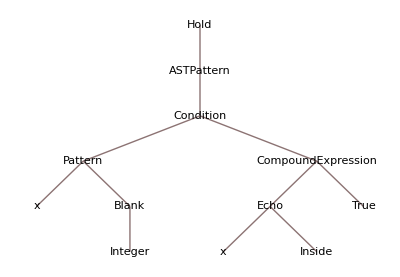

```mathematica
TreeForm[Hold[ASTPattern[x_Integer/;(Echo[x,"Inside"]; True)]]]
```

In this case, there is an x that's "lifted" out of the ASTPattern, which is why it appears as an AST node:

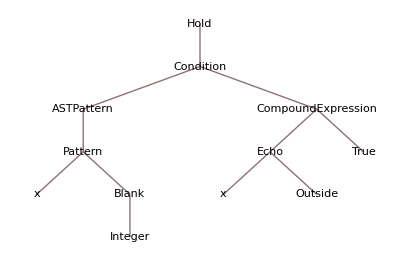

```mathematica
TreeForm[Hold[ASTPattern[x_Integer]/;(Echo[x,"Outside"]; True)]]
```

### Possible Issues

ASTPattern cannot generalize to all possible WL patterns:

```mathematica
ast=CodeParser`CodeParse["{f[1],f[1],f[1]}"]
```

CodeParser`ContainerNode[String,{CodeParser`CallNode[CodeParser`LeafNode[Symbol,List,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,2},{1,3}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,4},{1,5}}|>]},<|CodeParser`Source→{{1,2},{1,6}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,7},{1,8}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,9},{1,10}}|>]},<|CodeParser`Source→{{1,7},{1,11}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,12},{1,13}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,14},{1,15}}|>]},<|CodeParser`Source→{{1,12},{1,16}}|>]},<|CodeParser`Source→{{1,1},{1,17}}|>]},<||>]

```mathematica
FreeQ[ast,ASTPattern[{f[a_]..}]]
```

True

```mathematica
FreeQ[{f[1],f[1],f[1]},{f[a_]..}]
```

False

In this case, the pattern binding prevents matching, since the metadata will always be different between nodes:

```mathematica
Cases[ast,ASTPattern[{f[_]..}],Infinity]
```

{CodeParser`CallNode[CodeParser`LeafNode[Symbol,List,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,2},{1,3}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,4},{1,5}}|>]},<|CodeParser`Source→{{1,2},{1,6}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,7},{1,8}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,9},{1,10}}|>]},<|CodeParser`Source→{{1,7},{1,11}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,12},{1,13}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,14},{1,15}}|>]},<|CodeParser`Source→{{1,12},{1,16}}|>]},<|CodeParser`Source→{{1,1},{1,17}}|>]}

```mathematica
%[[1,2,All,3]]
```

{<|CodeParser`Source→{{1,2},{1,6}}|>,<|CodeParser`Source→{{1,7},{1,11}}|>,<|CodeParser`Source→{{1,12},{1,16}}|>}

Without any repeated binding this pattern will match:

```mathematica
FreeQ[ast,ASTPattern[{f[_]..}]]
```

False

Not all raw patterns are supported by ASTPattern:

```mathematica
node=CodeParser`CodeParse["f[x -> 1]"][[2,1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Rule,<||>],{CodeParser`LeafNode[Symbol,x,<|CodeParser`Source→{{1,3},{1,4}}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,8},{1,9}}|>]},<|CodeParser`Source→{{1,3},{1,9}}|>]},<|CodeParser`Source→{{1,1},{1,10}}|>]

```mathematica
patt=ASTPattern[f[OptionsPattern[]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,OptionsPattern|System`OptionsPattern,_],{},_]},_]

```mathematica
MatchQ[node,patt]
```

False

```mathematica
MatchQ[f[x->1],f[OptionsPattern[]]]
```

True

Unsupported patterns are represented verbatim:

```mathematica
MatchQ[CodeParser`CodeParse["f[OptionsPattern[]]"][[2,1]],patt]
```

True

```mathematica
MatchQ[f[OptionsPattern[]],Verbatim[f[OptionsPattern[]]]]
```

True

ASTPattern ignores the Unevaluated wrapper:

```mathematica
patt=ASTPattern[Unevaluated[1+1]]
```

CodeParser`LeafNode[Integer,2,_]

```mathematica
FreeQ[CodeParser`CodeParse["Hold[1+1]"],patt]
```

True

Use HoldPattern instead:

```mathematica
patt=ASTPattern[HoldPattern[1+1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],{CodeParser`LeafNode[Integer,1,_],CodeParser`LeafNode[Integer,1,_]},_]

```mathematica
FreeQ[CodeParser`CodeParse["Hold[1+1]"],patt]
```

False

ASTPattern must evaluate in order to create the desired pattern, so it should not be wrapped in HoldPattern:

```mathematica
MatchQ[CodeParser`CodeParse["1+1"][[2,1]],HoldPattern[ASTPattern[1+1]]]
```

False

Use HoldPattern within ASTPattern instead:

```mathematica
MatchQ[CodeParser`CodeParse["1+1"][[2,1]],ASTPattern[HoldPattern[1+1]]]
```

True

### Neat Examples

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

code parser

ast

ast matching

code search

parsing

metaprogramming

static analysis

syntax

patterns

code cases

file cases

### Categories

3D Visualization |  Accessibility
 Array Manipulation |  Cloud & Deployment
 Core Language & Structure |  Data Manipulation & Analysis
 Engineering Data & Computation |  External Interfaces & Connections
 Financial Data & Computation |  Geographic Data & Computation
 Geometry |  Graphs & Networks
 Higher Mathematical Computation |  Images
 Just For Fun |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Programming Utilities |  Repository Tools
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |  Wolfram Physics Project

### Related Symbols

MatchQ

Cases

Condition

PatternTest

Pattern

Verbatim

HoldPattern

### Related Resource Objects

GetKeyValuePattern

PatternSort

PatternBindings

PositionCases

PrintDefinitionCases

SymbolCases

PossibleNameQ

### Source/Reference Citation

Source, reference or citation information

### Links

ASTPattern | rhennigan/ResourceFunctions | GitHub

CodeParse | Wolfram Language Documentation

### Tests

#### Initialization

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> True ],
    KeyValuePattern[ "TestMode" -> True ],
    SameTest -> MatchQ,
    TestID -> "Set-MessageFailure-TestMode@@Definitions/ASTPattern/Tests.wlt:4,1-9,2"
]
```

```mathematica
VerificationTest[
    Needs[ "CodeParser`" ],
    Null,
    TestID -> "Initialize-Needs-CodeParser@@Definitions/ASTPattern/Tests.wlt:11,1-15,2"
]
```

```mathematica
VerificationTest[
    setDef // Attributes = { HoldFirst };
    setDef[ sym_Symbol ] :=
        If[ Context @ sym =!= Context @ ASTPattern,
            sym = Symbol @ StringJoin[
                      Context @ ASTPattern,
                      SymbolName @ Unevaluated @ sym
                  ];
            HoldPattern[ sym ] -> sym,
            Nothing
        ],
    Null,
    TestID -> "RF-Context-Helper-Definition@@Definitions/ASTPattern/Tests.wlt:17,1-30,2"
]
```

```mathematica
VerificationTest[
    setDef /@ { FromAST, EquivalentNodeQ },
    { }|{ _Rule, _Rule },
    SameTest -> MatchQ,
    TestID -> "RF-Context-Helper-Set@@Definitions/ASTPattern/Tests.wlt:32,1-37,2"
]
```

```mathematica
VerificationTest[
    testParse // Attributes = { HoldRest };

    testParse[ str_ ] := (CodeParse @ str)[[ 2, 1 ]];

    testParse[ str_, patt_ ] :=
        MatchQ[ testParse @ str, ASTPattern @ HoldPattern @ patt ];
    ,
    Null,
    TestID -> "TestParse-Definition@@Definitions/ASTPattern/Tests.wlt:39,1-49,2"
]
```

##### Context Check

```mathematica
VerificationTest[
    Context @ CodeParse,
    "CodeParser`",
    TestID -> "Context-CodeParse@@Definitions/ASTPattern/Tests.wlt:54,1-58,2"
]
```

```mathematica
VerificationTest[
    Context @ LeafNode,
    "CodeParser`",
    TestID -> "Context-LeafNode@@Definitions/ASTPattern/Tests.wlt:60,1-64,2"
]
```

```mathematica
VerificationTest[
    Context @ CallNode,
    "CodeParser`",
    TestID -> "Context-CallNode@@Definitions/ASTPattern/Tests.wlt:66,1-70,2"
]
```

```mathematica
VerificationTest[
    Context @ Source,
    "CodeParser`",
    TestID -> "Context-Source@@Definitions/ASTPattern/Tests.wlt:72,1-76,2"
]
```

#### ASTPattern

```mathematica
VerificationTest[
    ASTPattern[ _Integer ],
    (CallNode | LeafNode)[
        Integer | LeafNode[ Symbol, "Integer" | "System`Integer", _ ],
        _,
        _
    ],
    TestID -> "Leaf-Call@@Definitions/ASTPattern/Tests.wlt:81,1-89,2"
]
```

```mathematica
VerificationTest[
    ASTPattern[ _Integer? IntegerQ ],
    LeafNode[ Integer, _, _ ],
    TestID -> "Leaf-PatternTest@@Definitions/ASTPattern/Tests.wlt:91,1-95,2"
]
```

```mathematica
VerificationTest[
    ASTPattern @ x,
    LeafNode[ Symbol, "x" | Context @ x <> "x", _ ],
    TestID -> "Leaf-Symbol@@Definitions/ASTPattern/Tests.wlt:97,1-101,2"
]
```

```mathematica
VerificationTest[
    ASTPattern @ HoldPattern @ Identity[ _ ],
    CallNode[
        LeafNode[ Symbol, "Identity" | "System`Identity", _ ],
        { (CallNode|LeafNode)[ _, _, _ ] },
        _
    ],
    TestID -> "HoldPattern@@Definitions/ASTPattern/Tests.wlt:103,1-111,2"
]
```

```mathematica
VerificationTest[
    ASTPattern @ f[ ASTPattern[ _ ], ASTPattern[ _ ] ],
    ASTPattern @ f[ _, _ ],
    TestID -> "Invisible-Nested@@Definitions/ASTPattern/Tests.wlt:113,1-117,2"
]
```

```mathematica
VerificationTest[
    ASTPattern[ f[ ASTPattern[ _, a_ ], ASTPattern[ _, b_ ] ], c_ ],
    CodeParser`CallNode[
        CodeParser`LeafNode[ Symbol, "f" | Context @ f <> "f", _ ],
        {
            (CodeParser`CallNode | CodeParser`LeafNode)[ _, _, a_ ],
            (CodeParser`CallNode | CodeParser`LeafNode)[ _, _, b_ ]
        },
        c_
    ],
    TestID -> "Bound-Nested@@Definitions/ASTPattern/Tests.wlt:119,1-130,2"
]
```

##### Duplicate Pattern Symbols

```mathematica
VerificationTest[
    Count[ CodeParse[ "{{1,1},{2,2}}" ], ASTPattern @ { a_, a_ }, Infinity ],
    2,
    TestID -> "Duplicate-Pattern-Symbols-1@@Definitions/ASTPattern/Tests.wlt:135,1-139,2"
]
```

```mathematica
VerificationTest[
    Count[
        CodeParse[ "{{{1,1},{2,2}},{{1,1},{2,2}}}" ],
        ASTPattern @ { a_, a_ },
        Infinity
    ],
    5,
    TestID -> "Duplicate-Pattern-Symbols-2@@Definitions/ASTPattern/Tests.wlt:141,1-149,2"
]
```

```mathematica
VerificationTest[
    Cases[
        CodeParse[ "{{1,1,1},{1,1},{1,1,1,2},{2,2,2}}" ],
        ASTPattern[ expr: { a_, a_, a_ } ] :> FromAST @ expr,
        Infinity
    ],
    { { 1, 1, 1 }, { 2, 2, 2 } },
    TestID -> "Duplicate-Pattern-Symbols-3@@Definitions/ASTPattern/Tests.wlt:151,1-159,2"
]
```

##### Two Arguments

```mathematica
VerificationTest[
    ASTPattern[ id_String, as1_ ],
    id: (CallNode | LeafNode)[
        String | LeafNode[ Symbol, "String" | "System`String", _ ],
        _,
        as1_
    ],
    TestID -> "Two-Arguments@@Definitions/ASTPattern/Tests.wlt:164,1-172,2"
]
```

```mathematica
VerificationTest[
    Cases[
        CodeParse[ "VerificationTest[1 + 1, 2, TestID -> \"Addition\", SameTest -> SameQ]" ],
        ASTPattern[
            HoldPattern @ VerificationTest[
                __,
                TestID -> ASTPattern[ id_String, as1_ ],
                ___
            ] /; StringQ @ id,
            as2_
        ] :> Lookup[ { as1, as2 }, Source ],
        Infinity
    ],
    { { { { 1, 38 }, { 1, 48 } }, { { 1, 1 }, { 1, 68 } } } },
    TestID -> "Nested-Meta-Bindings@@Definitions/ASTPattern/Tests.wlt:174,1-189,2"
]
```

```mathematica
VerificationTest[
    ASTPattern[ id_, as1_ ],
    id: (CallNode | LeafNode)[ _, _, as1_ ],
    TestID -> "Meta-Unknown-Head@@Definitions/ASTPattern/Tests.wlt:191,1-195,2"
]
```

##### TestParse

```mathematica
VerificationTest[
    testParse[ "VerificationTest[x,y]", VerificationTest[ ___ ] ],
    True,
    TestID -> "TestParse-VerificationTest@@Definitions/ASTPattern/Tests.wlt:200,1-204,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[x,y]", f[ _, _ ] ],
    True,
    TestID -> "TestParse-Normal@@Definitions/ASTPattern/Tests.wlt:206,1-210,2"
]
```

```mathematica
VerificationTest[
    testParse[ "2.5", _Real ],
    True,
    TestID -> "TestParse-Atom-Real@@Definitions/ASTPattern/Tests.wlt:212,1-216,2"
]
```

```mathematica
VerificationTest[
    testParse[ "2", _Integer ],
    True,
    TestID -> "TestParse-Atom-Integer@@Definitions/ASTPattern/Tests.wlt:218,1-222,2"
]
```

```mathematica
VerificationTest[
    testParse[ "\"hello\"", _String ],
    True,
    TestID -> "TestParse-Atom-String@@Definitions/ASTPattern/Tests.wlt:224,1-228,2"
]
```

```mathematica
VerificationTest[
    testParse[ "x", _Symbol ],
    True,
    TestID -> "TestParse-Atom-Symbol@@Definitions/ASTPattern/Tests.wlt:230,1-234,2"
]
```

```mathematica
VerificationTest[
    With[ { expr = 2/3 }, testParse[ "2/3", expr ] ],
    True,
    TestID -> "TestParse-Atom-Rational@@Definitions/ASTPattern/Tests.wlt:236,1-240,2"
]
```

```mathematica
VerificationTest[
    With[ { expr = 2 + 3 I }, testParse[ "2 + 3 I", expr ] ],
    True,
    TestID -> "TestParse-Atom-Complex@@Definitions/ASTPattern/Tests.wlt:242,1-246,2"
]
```

```mathematica
VerificationTest[
    testParse[ "5", x_Integer ],
    True,
    TestID -> "TestParse-Pattern@@Definitions/ASTPattern/Tests.wlt:248,1-252,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[5]", e: f[ x_Integer ] ],
    True,
    TestID -> "TestParse-Nested-Pattern@@Definitions/ASTPattern/Tests.wlt:254,1-258,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[5]", f[ x_Integer ] /; Positive @ x ],
    True,
    TestID -> "TestParse-Condition-1@@Definitions/ASTPattern/Tests.wlt:260,1-264,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[5]", f[ x_Integer ] /; Negative @ x ],
    False,
    TestID -> "TestParse-Condition-2@@Definitions/ASTPattern/Tests.wlt:266,1-270,2"
]
```

```mathematica
VerificationTest[
    testParse[
        "VerificationTest[1+1, 2, TestID -> \"test\"]",
        VerificationTest[ __, TestID -> id_, ___ ] /; StringQ @ id
    ],
    True,
    TestID -> "TestParse-Condition-3@@Definitions/ASTPattern/Tests.wlt:272,1-279,2"
]
```

```mathematica
VerificationTest[
    testParse[
        "VerificationTest[1+1, 2, TestID -> Automatic]",
        VerificationTest[ __, TestID -> id_, ___ ] /; StringQ @ id
    ],
    False,
    TestID -> "TestParse-Condition-4@@Definitions/ASTPattern/Tests.wlt:281,1-288,2"
]
```

```mathematica
VerificationTest[
    testParse[ "5", _Integer? IntegerQ ],
    True,
    TestID -> "TestParse-PatternTest-1@@Definitions/ASTPattern/Tests.wlt:290,1-294,2"
]
```

```mathematica
VerificationTest[
    testParse[ "5", x_Integer? IntegerQ ],
    True,
    TestID -> "TestParse-PatternTest-2@@Definitions/ASTPattern/Tests.wlt:296,1-300,2"
]
```

```mathematica
VerificationTest[
    testParse[ "5", x_ /; IntegerQ @ x ],
    True,
    TestID -> "TestParse-PatternTest-3@@Definitions/ASTPattern/Tests.wlt:302,1-306,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[1.2]", f @ Except[ _Integer ] ],
    True,
    TestID -> "TestParse-Except-1@@Definitions/ASTPattern/Tests.wlt:308,1-312,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[1.2]", f @ Except[ _Real ] ],
    False,
    TestID -> "TestParse-Except-2@@Definitions/ASTPattern/Tests.wlt:314,1-318,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[1.2]", f @ Except[ _Integer, _Real ] ],
    True,
    TestID -> "TestParse-Except-3@@Definitions/ASTPattern/Tests.wlt:320,1-324,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[1.2]", f @ Except[ _Integer, _String ] ],
    False,
    TestID -> "TestParse-Except-4@@Definitions/ASTPattern/Tests.wlt:326,1-330,2"
]
```

```mathematica
VerificationTest[
    testParse[ "f[\"hello\"]", f @ Except[ _Integer, _String ] ],
    True,
    TestID -> "TestParse-Except-5@@Definitions/ASTPattern/Tests.wlt:332,1-336,2"
]
```

```mathematica
VerificationTest[
    testParse[ "{a,b,c,d,c,d,a,b}", { x__, PatternSequence[ c, d, c ], y__ } ],
    True,
    TestID -> "TestParse-PatternSequence-1@@Definitions/ASTPattern/Tests.wlt:338,1-342,2"
]
```

```mathematica
VerificationTest[
    testParse[ "{a,b,a,b,a,b,a,b,a,b}", { PatternSequence[ x_, x_ ].. } ],
    False,
    TestID -> "TestParse-PatternSequence-3@@Definitions/ASTPattern/Tests.wlt:344,1-348,2"
]
```

```mathematica
VerificationTest[
    testParse[ "{1,1,2,2}", ASTPattern @ { x_, x_, y_, y_ } ],
    True,
    TestID -> "Reused-Pattern-Bindings-1@@Definitions/ASTPattern/Tests.wlt:350,1-354,2"
]
```

```mathematica
VerificationTest[
    testParse[
        "1+1",
        ASTPattern @ HoldPattern[ ASTPattern[ 1 ] + ASTPattern[ 1 ] ]
    ],
    True,
    TestID -> "Nested-ASTPattern-Held@@Definitions/ASTPattern/Tests.wlt:356,1-363,2"
]
```

```mathematica
VerificationTest[
    testParse[ "{1,1}", ASTPattern[ { x_, x_ } /; IntegerQ @ x ] ],
    True,
    TestID -> "Reused-Bindings-Condition@@Definitions/ASTPattern/Tests.wlt:365,1-369,2"
]
```

#### FromAST

```mathematica
VerificationTest[
    Cases[
        CodeParse[ "VerificationTest[1 + 1, 2, TestID -> \"Addition\", SameTest -> SameQ]" ],
        ASTPattern[
            HoldPattern @ VerificationTest[
                __,
                TestID -> ASTPattern[ id_String, as1_ ],
                ___
            ] /; StringQ @ id,
            as2_
        ] :> FromAST @ id,
        Infinity
    ],
    { "Addition" },
    TestID -> "FromAST-Bindings@@Definitions/ASTPattern/Tests.wlt:374,1-389,2"
]
```

#### EquivalentNodeQ

```mathematica
VerificationTest[
    Enclose @ Apply[
        EquivalentNodeQ,
        ConfirmMatch[
            Cases[
                CodeParse[ "{f[x],f[x]}" ],
                ASTPattern[ _[ _ ] ],
                Infinity
            ],
            { _, _ }
        ]
    ],
    True,
    TestID -> "EquivalentNodeQ-1@@Definitions/ASTPattern/Tests.wlt:394,1-408,2"
]
```

#### Regression Tests

```mathematica
VerificationTest[
    testParse[ "{a,a,a}", ASTPattern[ { x: (_).. } /; SameQ @ x ] ],
    True,
    TestID -> "FromAST-Sequence-1@@Definitions/ASTPattern/Tests.wlt:413,1-417,2"
]
```

#### Future

```mathematica
Hold @ VerificationTest[
    testParse[ "{a,b,a,b,a,b,a,b,a,b}", { PatternSequence[ x_, y_ ].. } ],
    True,
    TestID -> "TestParse-PatternSequence-2@@Definitions/ASTPattern/Tests.wlt:422,8-426,2"
]
```

#### Cleanup

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> False ],
    KeyValuePattern[ "TestMode" -> False ],
    SameTest -> MatchQ,
    TestID -> "Reset-MessageFailure-TestMode@@Definitions/ASTPattern/Tests.wlt:431,1-436,2"
]
```

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.